```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*.ods"])//TableForm
```

data/t1_t_in_ms_i_in_V_cu005.ods
data/t1_t_in_ms_i_in_V_cu01.ods
data/t1_t_in_ms_i_in_V_cu02.ods
data/t2_CP_tau0k4ms_t_in_ms_i_in_V_cu005.ods
data/t2_CP_tau0k5ms_t_in_ms_i_in_V_cu01.ods
data/t2_CP_tau0k5ms_t_in_ms_i_in_V_cu02.ods
data/t2_MG_tau0k3ms_t_in_ms_i_in_V_cu005.ods
data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu01.ods
data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu02.ods
data/t2_spinecho_t_in_ms_i_in_V_cu005.ods
data/t2_spinecho_t_in_ms_i_in_V_cu01.ods
data/t2_spinecho_t_in_ms_i_in_V_cu02.ods
data/t2stern_t_in_mus_i_in_v_cu02.ods
data/t2stern_t_in_mus_i_in_v_mineralol.ods

```mathematica
(t2stoel=First@Import["data/t2stern_t_in_mus_i_in_v_mineralol.ods"])//TableForm;
(t2stcu02=First@Import["data/t2stern_t_in_mus_i_in_v_cu02.ods"])//TableForm;
t1005=First@Import["data/t1_t_in_ms_i_in_V_cu005.ods"];
t101=First@Import["data/t1_t_in_ms_i_in_V_cu01.ods"];
t102=First@Import["data/t1_t_in_ms_i_in_V_cu02.ods"];
spin005=First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu005.ods"];
spin01=First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu01.ods"];
spin02=First@Import["data/t2_spinecho_t_in_ms_i_in_V_cu02.ods"];
mg005=First@Import["data/t2_MG_tau0k3ms_t_in_ms_i_in_V_cu005.ods"];
mg01=First@Import["data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu01.ods"];
mg02=First@Import["data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu02.ods"];
cp005=First@Import["data/t2_MG_tau0k4ms_t_in_ms_i_in_V_cu005.ods"];
cp01=First@Import["data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu01.ods"];
cp02=First@Import["data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu02.ods"];
```

Import::nffil: File not found during Import.

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

```mathematica
FitFit[dat_,as_,bs_,cs_]:=(fitt=NonlinearModelFit[dat,Abs[b*Exp[ -x/a]+c],{{a,as},{b,bs},{c,cs}},x];
Show[ListPlot[dat],Plot[Normal@fitt,{x,-1000,2000},PlotRange->All]])
```

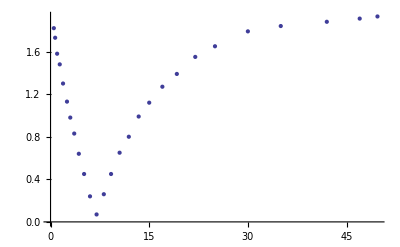

```mathematica
FitFit[First@Import[files[[2]]],15,-2,1.7]
```

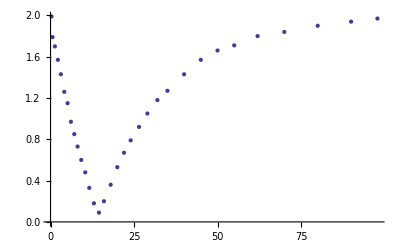

data/t1_t_in_ms_i_in_V_cu005.ods

-Graphics-

data/t1_t_in_ms_i_in_V_cu01.ods

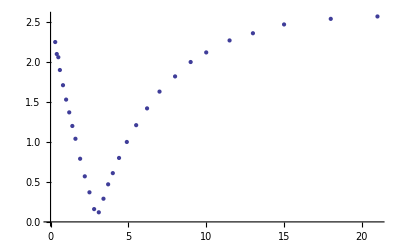

data/t1_t_in_ms_i_in_V_cu02.ods

```mathematica
For[i=1,i≤3,i++,Print[FitFit[First@Import[files[[i]]],15,-2.5,1.7]];Print[files[[i]]]]
```

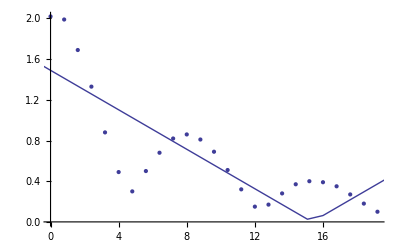

data/t2_CP_tau0k4ms_t_in_ms_i_in_V_cu005.ods

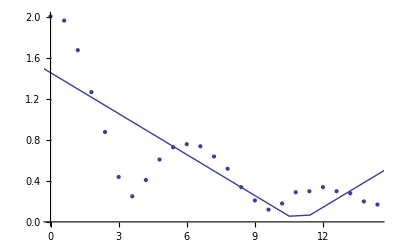

data/t2_CP_tau0k5ms_t_in_ms_i_in_V_cu01.ods

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

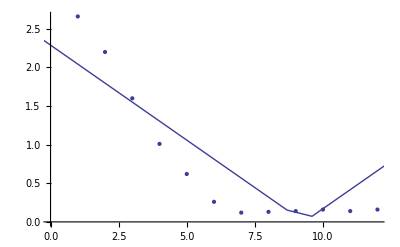

data/t2_CP_tau0k5ms_t_in_ms_i_in_V_cu02.ods

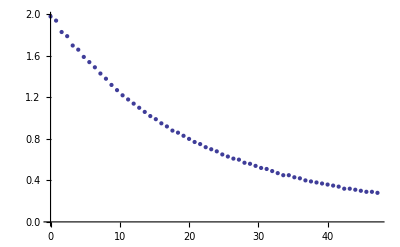

data/t2_MG_tau0k3ms_t_in_ms_i_in_V_cu005.ods

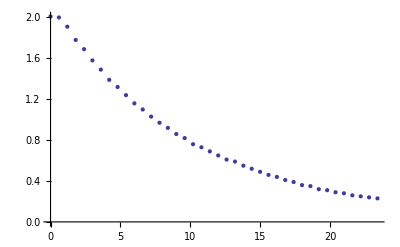

data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu01.ods

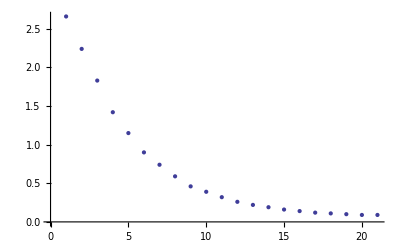

data/t2_MG_tau0k5ms_t_in_ms_i_in_V_cu02.ods

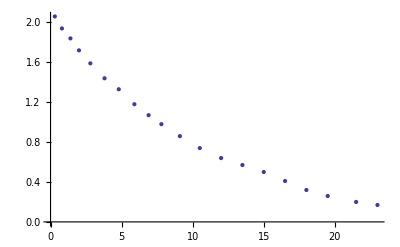

data/t2_spinecho_t_in_ms_i_in_V_cu005.ods

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

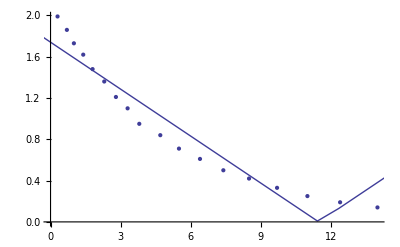

data/t2_spinecho_t_in_ms_i_in_V_cu01.ods

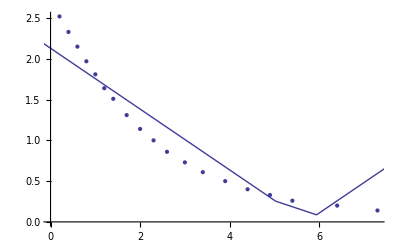

data/t2_spinecho_t_in_ms_i_in_V_cu02.ods

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

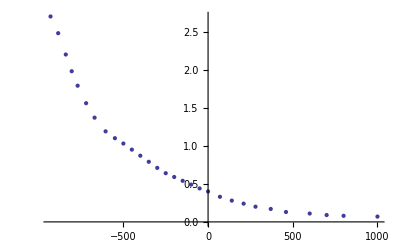

data/t2stern_t_in_mus_i_in_v_cu02.ods

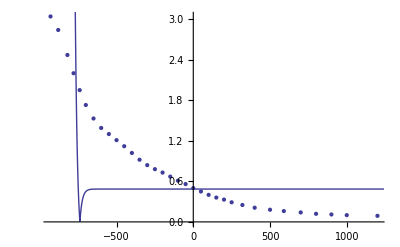

data/t2stern_t_in_mus_i_in_v_mineralol.ods

```mathematica
For[i=4,i≤Length@files,i++,Print[FitFit[First@Import[files[[i]]],15,2.5,1.7]];Print[files[[i]]]]
```